```mathematica
(* Parametros del sistema *)
gamma=3;
w=1;
w0=10;
```

```mathematica
(* Funciones dinámicas del sistema *)
F[{p_,q_,P_,Q_}]:={-gamma*Q*Sqrt[4-P^2-Q^2]-q*w,
p*w,
(gamma*q*Q^2)/(Sqrt[4-P^2-Q^2])-gamma*q*Sqrt[4-P^2-Q^2]-Q*w0,
P*w0-gamma*P*q*Q/(Sqrt[4-P^2-Q^2])}
```

```mathematica
JacobianMatrix[f_List,v_List]:=Outer[D,f,v]
J = JacobianMatrix[F[{Subscript[y,1][t],Subscript[y,2][t],Subscript[y,3][t],Subscript[y,4][t]}],{Subscript[y,1][t],Subscript[y,2][t],Subscript[y,3][t],Subscript[y,4][t]}];
```

```mathematica
Phi=Table[{Subscript[y,k][t],Subscript[y,k+1][t],Subscript[y,k+2][t],Subscript[y,k+3][t]},{k,5,20,4}];
```

```mathematica
DPhi=Flatten[J.Phi];
```

```mathematica
EQ4= Table[D[Subscript[y,k][t],{t,1}]==

F[{Subscript[y,1][t],Subscript[y,2][t],Subscript[y,3][t],Subscript[y,4][t]}][[k]],{k,1,4}];
```

```mathematica
EQ12=Table[D[Subscript[y,k][t],{t,1}] == 
DPhi[[k-4]],{k,5,20}];

fun[k_]:= If[k==5 || k==10 || k==15 || k==20,1,0]
```

```mathematica
(* Determinar la energía mínima con la que las condiciones iniciales proporcionadas son válidas *)

(* Defino condiciones iniciales para P y Q *)
P0=0;
Q0=-1.201850425154663;
H[{p_,q_,P_,Q_}]=w0/2*(Q^2+P^2)+w/2*(p^2+q^2)+gamma*q*Q*Sqrt[4-Q^2-P^2]-w0;
(*J'z/j*)
f=gamma/(Sqrt[w*w0]/2);
Jz[{p_,q_,P_,Q_}]=(1/2*(Q^2+P^2)-1+Sqrt[f^2*w/w0]*q*Q*Sqrt[1-1/4*(Q^2+P^2)])/(Sqrt[1+f^2*w/w0*q^2]);
Emin=Minimize[H[{p,q,P0,Q0}],{p,q}][[1]];
MinVariables=N[Minimize[H[{p,q,P,Q}],{p,q,P,Q}][[2]]];
Emintotal=N[Minimize[H[{p,q,P,Q}],{p,q,P,Q}][[1]]];
Jmintotal=NMinimize[Jz[{p,q,P,Q}],{q,p,P,Q}][[1]];
Jmin=NMinimize[Jz[{p,q,P0,Q0}],{q,p}][[1]];
Print["Con estos parametros, la energía mínima del sistema es " ,Emintotal/w0," w0"]
Print["Con estos parametros, la energía mínima del sistema se consigue en " ,MinVariables, ". El valor de Jz para la energía mínima es ",Jz[MinVariables[[All,2]]]]
Print["Con estas condiciones iniciales, la energía mínima de la configuración es " ,Emin/w0," w0"]
Print["La jz mínima es " ,Jmintotal, ". Con estas condiciones iniciales, la jz mínima es " ,Jmin];
```

Con estos parametros, la energía mínima del sistema es -1.93889 w0

Con estos parametros, la energía mínima del sistema se consigue en {p→0.,q→5.76387,P→0.,Q→-1.20185}. El valor de Jz para la energía mínima es -1.

Con estas condiciones iniciales, la energía mínima de la configuración es -1.93889 w0

La jz mínima es -1.. Con estas condiciones iniciales, la jz mínima es -1.

```mathematica
(* Comprobación de que las condiciones que elegimos son compatibles con soluciones reales *)
jz=Jz[MinVariables[[All,2]]];
Einicial=-0.999985;
A=1/2*(Q0^2+P0^2);
B=Sqrt[f^2*w/w0]*Q0*Sqrt[1-1/4*(Q0^2+P0^2)];
c=f^2*w/w0;
If[B^2+c*A^2-c*jz >0 &&  (Q0^2+P0^2)<4, Print["La solución q será real"], Print["La solución q no será real, pon otras condiciones"]];
q0=Re[Solve[Jz[{0,q,P0,Q0}] == jz,q][[1]][[1]][[2]]];
e=Solve[- gamma*Q0*Sqrt[4-Q0^2-P0^2]*q0-w0/2*(Q0^2+P0^2)-w/2*q0^2+w0+ e0 == 0, e0][[1]][[1]][[2]];
Print["La energía mínima para que estas condiciones iniciales sean válidas es: ",e/w0," w0"]
```

La solución q será real

La energía mínima para que estas condiciones iniciales sean válidas es: -1.93889 w0

```mathematica
qs={};
pasos=1;
precision=10;

(* Defino condiciones iniciales para P y Q *)
T=500; (* Tiempo de trayectoria *)
energy=Einicial*w0;
p0=Solve[w/2*q0^2 + gamma*Q0*Sqrt[4-Q0^2-P0^2]*q0+w0/2*(Q0^2+P0^2)+w/2*p^2-w0== energy,p][[1]][[1]][[2]];
YI12= Table[Subscript[y,k][0] == fun[k],{k,5,20}];
YI4 ={Subscript[y,1][0]==p0 , Subscript[y,2][0]==q0, Subscript[y,3][0]==P0,Subscript[y,4][0]==Q0 };
(* Solucion *)
sol=NDSolve[Join[EQ4,EQ12,YI4,YI12],Table[Subscript[y,k][t],{k,1,20}],{t,0,T}, StepMonitor->Sow[x], Method->"StiffnessSwitching",
MaxSteps->Infinity,MaxStepSize->10^-2,AccuracyGoal->5];
qvalues={};
energy ={};
jzs={};
funcq=sol[[1]][[2]][[2]][[0]];
funcp = sol[[1]][[1]][[2]][[0]];
funcP =sol[[1]][[3]][[2]][[0]];
funcQ = sol[[1]][[4]][[2]][[0]];
For[j=0,j<T*precision,j++,qvalues=Append[qvalues,funcq[j/precision]]];
For[j=0, j<T*precision, j++ , jzs= Append[jzs,Jz[{funcp[j/precision],funcq[j/precision],funcP[j/precision],funcQ[j/precision]}]]];
For[j=0, j<T*precision, j++ , energy= Append[energy,H[{funcp[j/precision],funcq[j/precision],funcP[j/precision],funcQ[j/precision]}]]]
```

```mathematica
(* Lista para que mathematica sepa dibujar*)

plotlist={};
For[i=0,i<T*precision,i++,plotlist= Append[plotlist,{i/precision,qvalues[[i+1]]}]];
```

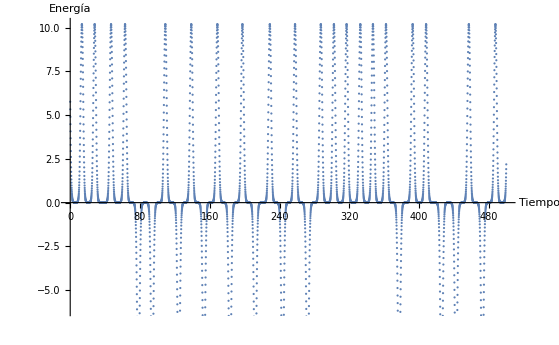

```mathematica
ListPlot[plotlist, AxesLabel->{"Tiempo","Energía"}]
```

```mathematica
(* Lista para que mathematica sepa dibujar*)
plotlist2={}
For[i=0,i<T*precision,i++,plotlist2= Append[plotlist2,{i/precision,energy[[i+1]]}]];
```

{}

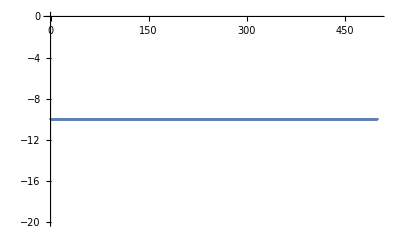

```mathematica
ListPlot[plotlist2]
```

{}

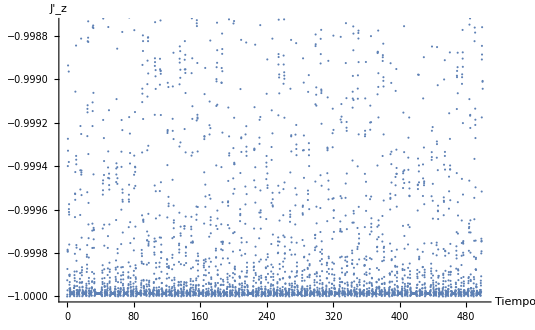

```mathematica
plotlist3={}
For[i=0,i<T*precision,i++,plotlist3= Append[plotlist3,{i/precision,jzs[[i+1]]}]];
ListPlot[plotlist3,AxesLabel->{"Tiempo","J'_z"}]
```